# Analyzing Peg Solitaire Game Boards using Multiway Graphs

Peg Solitaire, also known as Cracker Barrel, is a game played on a board consisting of a number of holes of which all but one are filled with a peg. These boards are usually symmetrical, in shapes such as equilateral  triangles or thick crosses. The goal of the game is to remove all but one peg by jumping pegs over each other, from one side of a peg hole to a free space, removing the peg which was jumped over.

[ graphic of basic peg solitaire boards (triangle and square) ]

This project hopes to model different game boards of peg solitaire, with different board shapes and starting arrangements of pegs, and use their multiway graphs to find a board shape in which there is only one possible solution, or where you must play a perfect game to be able to win, and to see if there are board shapes wherein the game is impossible to solve.

#### Node Layout Generation

```mathematica
graphgen[start_,moves_ ]:={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[moves],
{start},
UnsameQ@@#&,2]
```

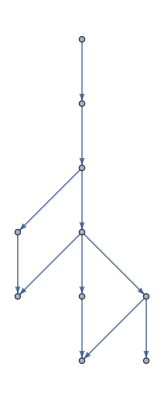

```mathematica
graphgen[{1,1,0,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}]
```

#### Generating Unique Starting Boards

```mathematica
(* maps each coordinate to a "name" *)
coordnames[coords_] := MapIndexed[#1->#2[[1]]&,coords]
```

```mathematica
(* gets ALL possible starting boards of a given set of coords *)
visstartingboards[coords_]:= Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][state],{state, Permutations[Append[Table[1, Length[coords]-1],0]]}]
```

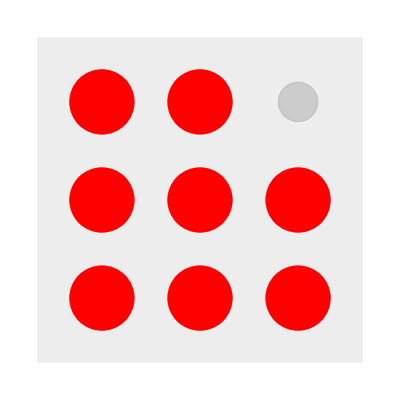
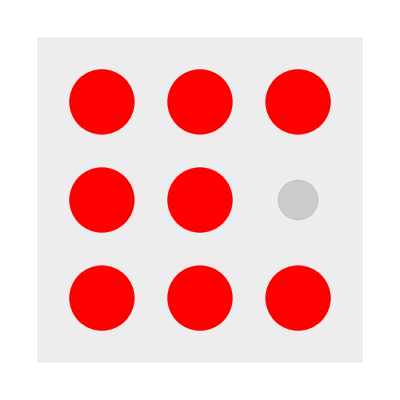
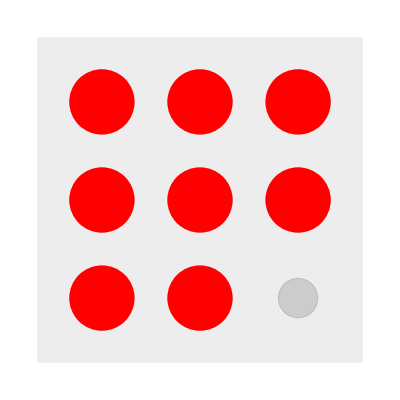
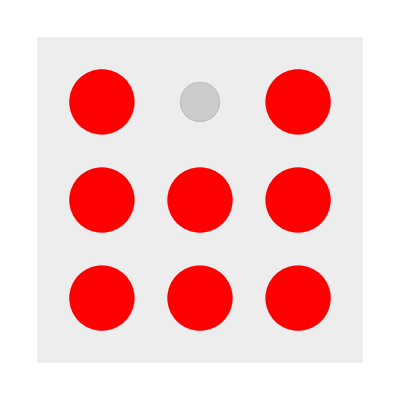
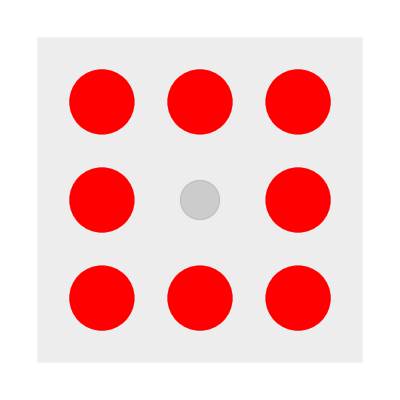
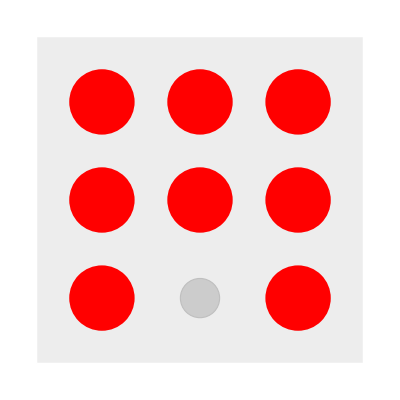
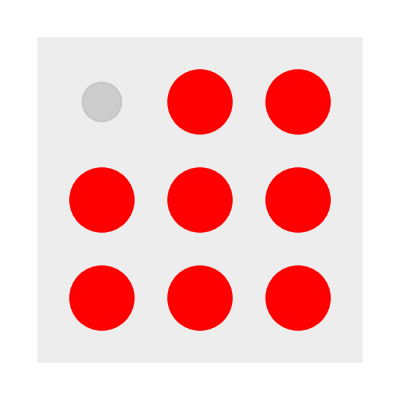
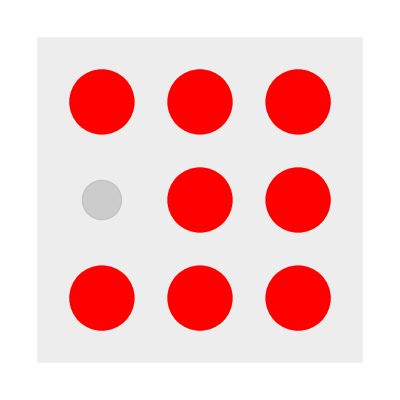

```mathematica
visstartingboards[{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}]
```

```mathematica
(* compares two images and checks if they are the same *)
compareImg[img1_, img2_]:=If[Length[DominantColors[ImageDifference[ImageRotate[img1, 90 Degree], img2]]] ==1 || Length[DominantColors[ImageDifference[ImageRotate[img1, 180 Degree], img2]]]==1 || Length[DominantColors[ImageDifference[ImageRotate[img1, 270 Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageReflect[img1], img2]]]==1||
Length[DominantColors[ImageDifference[ImageReflect[img1, Left], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],90Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],180Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],270Degree], img2]]]==1,
True, False]
```

```mathematica
compareImg[-Graphics-,-Graphics-]
```

False

```mathematica
compareImg[-Graphics-,-Graphics-]
```

True

```mathematica
(* checks if an image is already represented in a list *)
uniqueImg[img_, uniques_] := Which[Length[uniques] ==1, Not[compareImg[img, uniques[[1]]]],
Position[compareImg@@@Partition[Riffle[uniques,img, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
(* create a list of unique elements *)
getUnique[stateimglist_] := 
Block[{states = stateimglist, uniques = {stateimglist[[1]]}},
If[uniqueImg[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

```mathematica
getUnique[visstartingboards[{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}]]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Creating Multiway Graphs with Visuals

```mathematica
(* create multiway graphs given a set of coordinates for a board, the starting positions of pegs, and all of the possible moves *)

(* multiwaygraph[list of coords (no names), starting state, possible moves] *)
multiwaygraph[coords_, start_, moves_] := Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]
```

```mathematica
(* create multiway graphs without duplicate boards given a set of coordinates for a board, the starting positions of pegs, all of the possible moves, and a square board *)

(* multiwaygraph2[list of coords (no names), starting state, possible moves] *)
multiwaygraph2[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareImg[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#1], {{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#2]] ==True&]]
]
```

```mathematica
coords = {{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}};
start = {1,0,1,1,1,1,1,1};
moves = {{1,4,6},{7,6,5},
{3,5,8},{4,3,2}};
```

multiway graph testing !

```mathematica
(* simple "square" board *)
multiwaygraph[coords,start,moves]
```

-Graphics-

```mathematica
(* simple triangle *)
multiwaygraph[{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2}},{1,1,1,1,1,0},{{1,3,6},{1,2,4},{4,5,6}}]
```

-Graphics-

```mathematica
(* simple square using multiway graph 1*)
multiwaygraph[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}},{0,1,1,1,1,1,1,1,1},{{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}}]
```

-Graphics-

```mathematica
(* simple square using multiway graph 2*)
multiwaygraph2[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}},{0,1,1,1,1,1,1,1,1},{{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}}]
```

-Graphics-

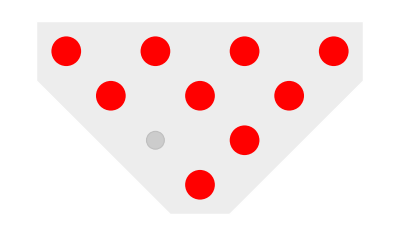
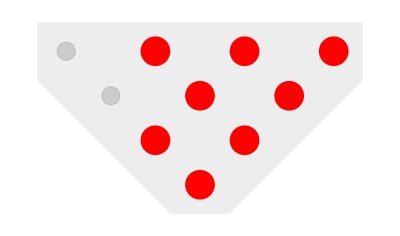
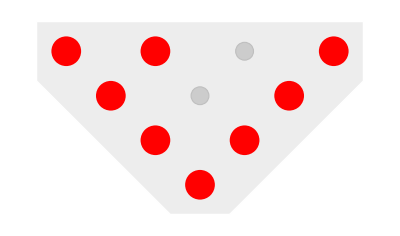
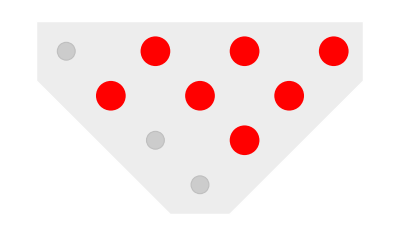
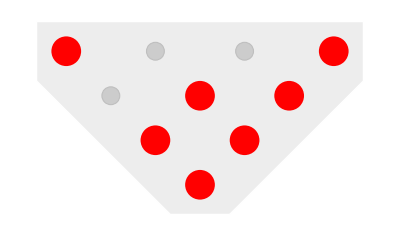
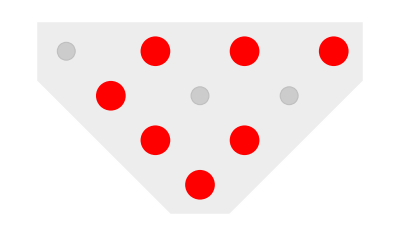
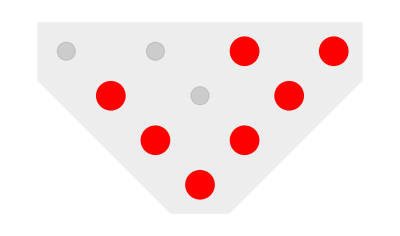
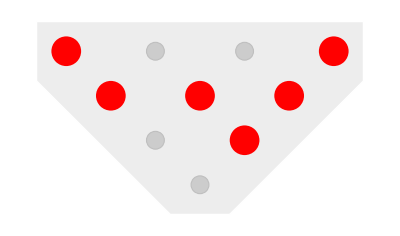

```mathematica
(* larger triangle *)
multiwaygraph[{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}},{1,0,1,1,1,1,1,1,1,1},{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{4,5,6},{7,8,9}}]
```

```mathematica
multiwaygraph2[{{3,1},{4,1},{5,1},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7}},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{{1,2,3},{1,4,9},{2,5,10},{3,2,1},{3,6,11},{4,5,6},{4,9,16},{5,10,17},{6,5,4},{6,11,18},{7,8,9},{7,14,21},{8,9,10},{8,15,22},{9,4,1},{9,8,7},{9,10,11},{9,16,23},{10,5,2},{10,9,8},{10,11,12},{10,17,24},{11,6,3},{11,10,9},{11,12,13},{11,18,25},{12,11,10},{12,19,26},{13,12,11},{13,20,27},{14,15,16},{15,16,17},{16,9,4},{16,15,14},{16,17,18},{16,23,28},{17,10,5},{17,16,15},{17,18,19},{17,24,29},{18,11,6},{18,17,16},{18,19,20},{18,25,30},{19,18,17},{20,19,18},{21,14,7},{21,22,23},{22,15,8},{22,23,24},{23,16,9},{23,22,21},{23,24,25},{23,28,31},{24,17,10},{24,23,22},{24,25,26},{24,29,32},{25,18,11},{25,24,23},{25,26,27},{25,30,33},{26,19,12},{26,25,24},{27,20,13},{27,26,25},{28,23,16},{28,29,30},{29,24,17},{30,25,18},{30,29,28},{31,28,23},{31,32,33},{32,29,24},{33,30,25},{33,32,31}}]
```

#### Calculating Possible Moves

triangle data:

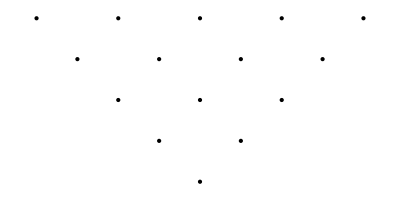
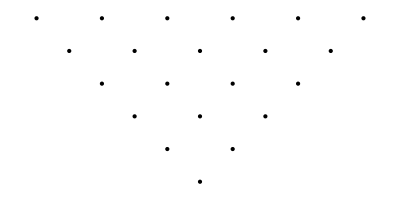
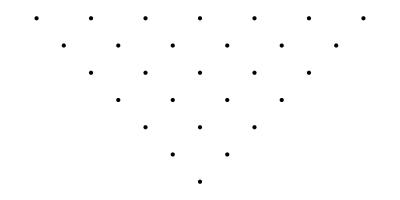
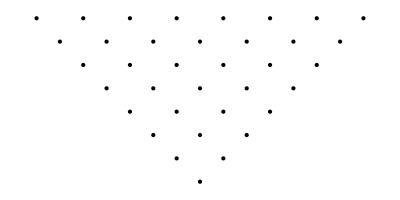
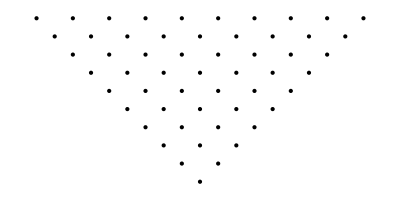
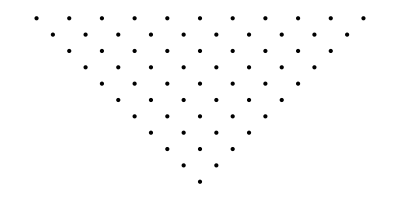
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
triangle = {makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2}}],
makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}}], makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9},{10,10},{8,10},{6,10},{4,10},{2,10},{0,10},{-2,10},{-4,10},{-6,10},{-8,10},{-10,10}}]}
```

square data:

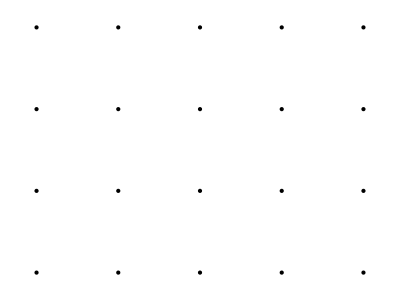
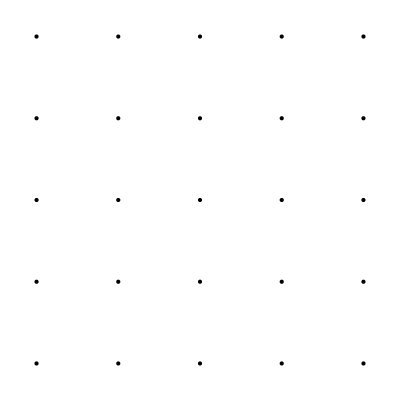
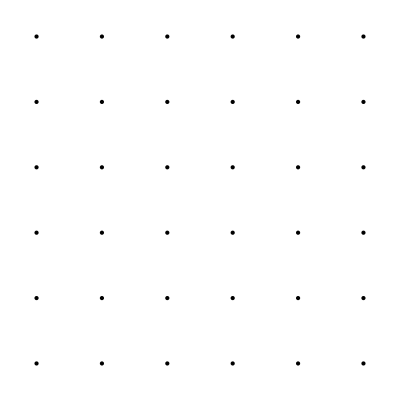
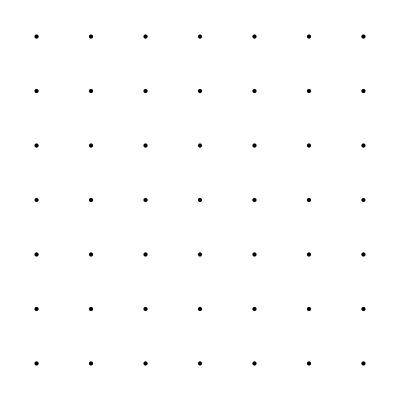
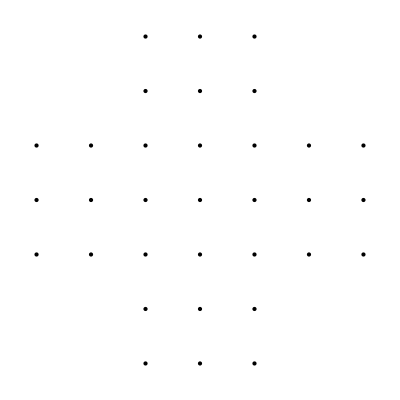
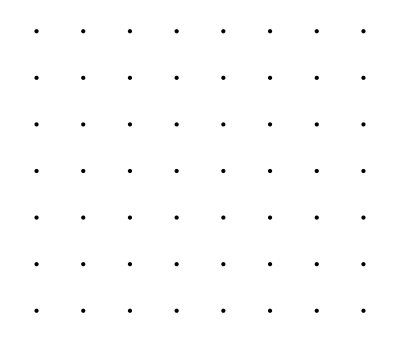
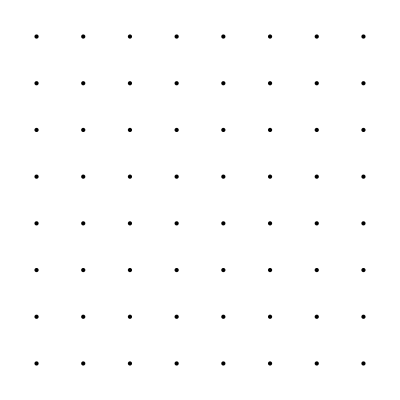
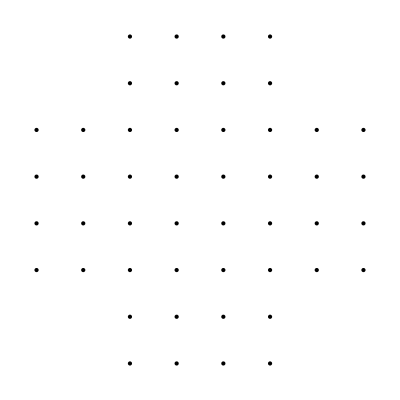
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
square = {makeimg[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2}, {1,3}, {2,3},{3,3}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{1,4},{2,4},{3,4},{4,4}}],makeimg[{{2,1},{3,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{2,4},{3,4}}] ,makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{1,5},{2,5},{3,5},{4,5},{5,5}}], makeimg[{{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{2,5},{3,5},{4,5}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6}}],makeimg[{{3,1},{4,1},{3,2},{4,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{3,5},{4,5},{3,6},{4,6}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7}}],makeimg[{{3,1},{4,1},{5,1},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8}}],makeimg[{{3,1},{4,1},{5,1},{6,1},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{3,7},{4,7},{5,7},{6,7},{3,8},{4,8},{5,8},{6,8}}]}
```

```mathematica
(* makes an image that shows points given by a list of coordinates *)
makeimg[points_ ] := 
Graphics[{PointSize[Large],Point[Table[p,{p,points}]]}]
```

```mathematica
checkshape = Classify[<|"square" -> square, "triangle" ->triangle|>]
```

ClassifierFunction[…]

```mathematica
checkshape[makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{9,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{9,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{9,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{9,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{9,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{9,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8}}]]
```

square

```mathematica
(* calculates the points next to a specified peg given the coordinates of a square*)
getNear[coords_, peg_, shape_String:"square", normal_Booleans:True]/; shape=="square"&& normal==True := Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 && (coord[[1]] == peg[[1]] || coord[[2]] == peg[[2]]), coord],{coord, coords}], ListQ]]
```

```mathematica
(* getNear but for a triangle *)
getNear[coords_, peg_, shape_String:"square", normal_Booleans:True]/; shape=="triangle"&& normal == True := Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 || And[peg[[2]]==coord[[2]],EuclideanDistance[peg, coord] == 2], coord],{coord, coords}], ListQ]]
```

```mathematica
(* given a peg and a list of coordinates, finds all the possible moves that peg could be in *)
pegMoves[initalpeg_, coordlist_, normal_Booleans:True]/;normal ==True :=Module[{peg = initalpeg, coords = coordlist, moves = {}, peg2s, peg3s},
peg2s = getNear[coords, peg, checkshape[makeimg[coords]]];
peg3s = Table[{peg2[[1]]+(peg2[[1]] - peg[[1]]), peg2[[2]]+(peg2[[2]]-peg[[2]])}, {peg2, peg2s}];
Select[Table[If[Position[coords,peg3s[[i]]] != {},{peg, peg2s[[i]], peg3s[[i]]}], {i, Range[Length[peg2s]]}], ListQ]
]
```

```mathematica
pegMoves[{3,3}, {{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}]
```

{{{3,3},{2,2},{1,1}},{{3,3},{1,3},{-1,3}}}

```mathematica
(* maps through all pegs in a peg list and find all possible moves *)
allMoves[coordlist_,normal_:True]/;normal := Module[{coords = coordlist, moves = {}},
ResourceFunction["JoinTo"][moves, pegMoves[#, coords] /. coordnames[coords] &/@ coords];
DeleteDuplicates[Flatten[moves,1], Length[#1∪#2] ==3 &]
]
```

```mathematica
allMoves[{{3,1},{4,1},{5,1},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7}}]
```

{{1,2,3},{1,4,9},{2,5,10},{3,2,1},{3,6,11},{4,5,6},{4,9,16},{5,10,17},{6,5,4},{6,11,18},{7,8,9},{7,14,21},{8,9,10},{8,15,22},{9,4,1},{9,8,7},{9,10,11},{9,16,23},{10,5,2},{10,9,8},{10,11,12},{10,17,24},{11,6,3},{11,10,9},{11,12,13},{11,18,25},{12,11,10},{12,19,26},{13,12,11},{13,20,27},{14,15,16},{15,16,17},{16,9,4},{16,15,14},{16,17,18},{16,23,28},{17,10,5},{17,16,15},{17,18,19},{17,24,29},{18,11,6},{18,17,16},{18,19,20},{18,25,30},{19,18,17},{20,19,18},{21,14,7},{21,22,23},{22,15,8},{22,23,24},{23,16,9},{23,22,21},{23,24,25},{23,28,31},{24,17,10},{24,23,22},{24,25,26},{24,29,32},{25,18,11},{25,24,23},{25,26,27},{25,30,33},{26,19,12},{26,25,24},{27,20,13},{27,26,25},{28,23,16},{28,29,30},{29,24,17},{30,25,18},{30,29,28},{31,28,23},{31,32,33},{32,29,24},{33,30,25},{33,32,31}}

```mathematica
Length[{{1,2,3},{1,4,9},{2,5,10},{3,2,1},{3,6,11},{4,5,6},{4,9,16},{5,10,17},{6,5,4},{6,11,18},{7,8,9},{7,14,21},{8,9,10},{8,15,22},{9,4,1},{9,8,7},{9,10,11},{9,16,23},{10,5,2},{10,9,8},{10,11,12},{10,17,24},{11,6,3},{11,10,9},{11,12,13},{11,18,25},{12,11,10},{12,19,26},{13,12,11},{13,20,27},{14,15,16},{15,16,17},{16,9,4},{16,15,14},{16,17,18},{16,23,28},{17,10,5},{17,16,15},{17,18,19},{17,24,29},{18,11,6},{18,17,16},{18,19,20},{18,25,30},{19,18,17},{20,19,18},{21,14,7},{21,22,23},{22,15,8},{22,23,24},{23,16,9},{23,22,21},{23,24,25},{23,28,31},{24,17,10},{24,23,22},{24,25,26},{24,29,32},{25,18,11},{25,24,23},{25,26,27},{25,30,33},{26,19,12},{26,25,24},{27,20,13},{27,26,25},{28,23,16},{28,29,30},{29,24,17},{30,25,18},{30,29,28},{31,28,23},{31,32,33},{32,29,24},{33,30,25},{33,32,31}}]
```

76

#### Removing “Duplicate” Boards Using Matrices

```mathematica
compareSqrList[list1_, list2_] := Module[{length = Sqrt[Length[list1]]},
lists1 = Partition[list1, length];
lists2 = Partition[list2, length];
If[Transpose @(Reverse/@lists1)==lists2 ||
Reverse/@(Transpose @lists1)==lists2 ||
Transpose @(Reverse/@(Transpose @(Reverse/@lists1)))==lists2 ||
Transpose @(Reverse/@(Transpose @lists1)) == lists2||
Reverse/@(Transpose @(Reverse/@lists1)) == lists2||
Transpose @lists1 ==lists2 ||
Reverse/@lists1 ==lists2
,True,False]
]
```

```mathematica
compareSqrList[{0,0,0,1,0,0,1,1,1}, {0,0,0,0,0,1,1,1,1}]
```

True

```mathematica
compareSqrList[{0,1,1,1,1,1,1,1,1}, {1,1,1,0,1,1,1,1,1}]
```

False

```mathematica
compareSqrList[{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, {1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1}]
```

True

```mathematica
(* checks if a board is already represented in a list *)
uniqueboard[board_, uniques_] := Which[Length[uniques] ==1, Not[compareSqrList[board, uniques[[1]]]],
Position[compareSqrList@@@Partition[Riffle[uniques,{board}, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
(* create a list of unique elements *)
getUniqueBoards[statelist_] := 
Block[{states = statelist, uniques = {statelist[[1]]}},
If[uniqueboard[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

```mathematica
(* create multiway graphs without duplicate boards given a set of coordinates for a board, the starting positions of pegs, all of the possible moves, and a square board *)

(* multiwaygraph3[list of coords (no names), starting state, possible moves] *)
multiwaygraph3[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareSqrList[#1,#2] ==True&]]
]
```

```mathematica
fourcoords = {{1,1},{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{1,4},{2,4},{3,4},{4,4}};
fourmoves = allMoves[fourcoords];
```

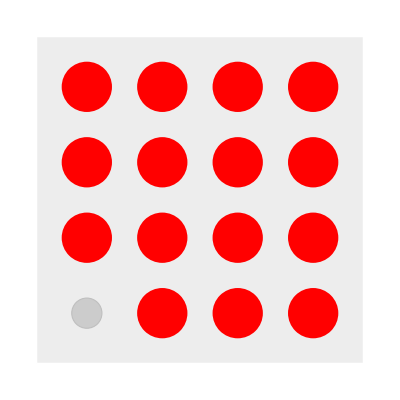
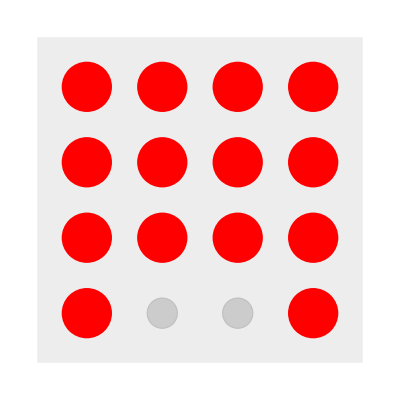
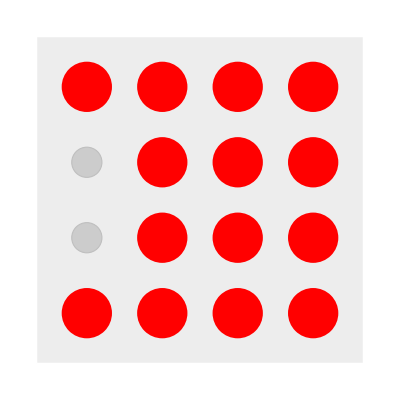
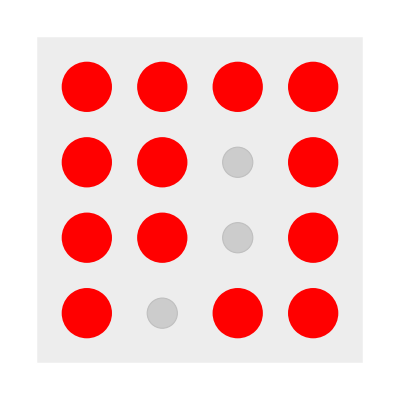
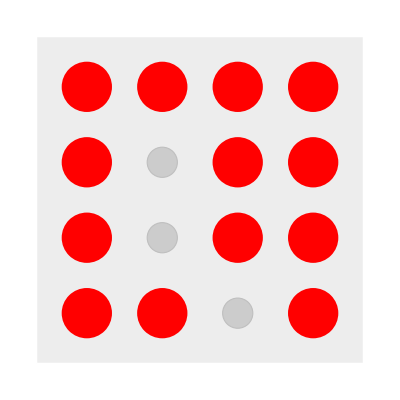
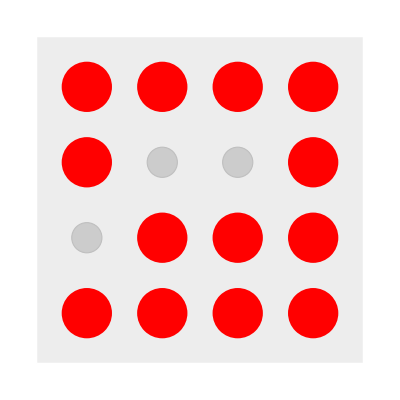
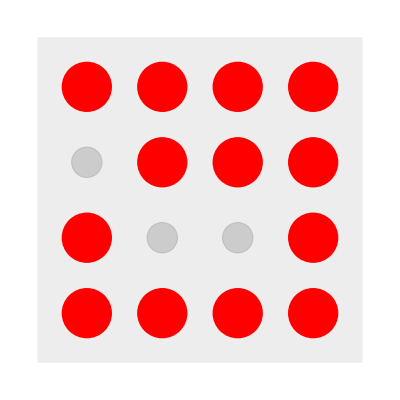
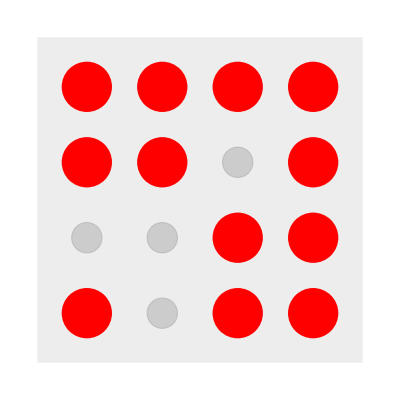

```mathematica
multiwaygraph[fourcoords,{ 0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, fourmoves]
```

```mathematica
multiwaygraph3[fourcoords,{ 0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, fourmoves]
```

-Graphics-

```mathematica
threecoords = {{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}};
threemoves = allMoves[threecoords];
```

```mathematica
multiwaygraph[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves ] //Timing
```

{0.006605,-Graphics-}

```mathematica
multiwaygraph2[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves ] // Timing
```

{111.861,-Graphics-}

```mathematica
multiwaygraph3[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves ] // Timing
```

{0.029719,-Graphics-}

#### Analyzing 3 x 3 boards

```mathematica
Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[threecoords]][perm], {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* all "starting board" states which lead to a multiway graph longer than 2 *)
SortBy[Select[Table[If[VertexCount[multiwaygraph3[threecoords, state, threemoves]]>2, multiwaygraph3[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* all "starting board" states which lead to a solution *)
SortBy[Select[Table[If[VertexCount[multiwaygraph3[threecoords, state, threemoves]]>1 && Length[Position[VertexList[multiwaygraph3[threecoords, state, threemoves]][[-1]],1]]==1, multiwaygraph3[threecoords, state, threemoves]], {state, Table[perm, {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]}],GraphQ], VertexCount]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cropGraph[fullgraph_, maxpins_, coords_] :=Graph[Graph[Cases[Table[If[ Position[Select[Table[If[Length[Position[vertex,1]]<=maxpins,vertex], {vertex, VertexList[fullgraph]}],ListQ],edge[[1]]]!={}, edge],{edge, EdgeList[fullgraph]}], Except[Null]]],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3, VertexCoordinates->Rule @@@Partition[Riffle[VertexList[fullgraph],(VertexCoordinates/. AbsoluteOptions[fullgraph,VertexCoordinates])],2]]
```

```mathematica
cropGraph2[-Graphics-,4, threecoords]
```

-Graphics-

```mathematica
cropGraph2[-Graphics-,3,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}]
```

-Graphics-

```mathematica
Graph[cropGraph[-Graphics-,4,fourcoords],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][
#2],#1,Center,#3]&),VertexSize->2]
```

-Graphics-

#### 3 x 3 Boards with Holes

```mathematica
holeBoardCoords[coords_, state_] := Join[coordnames[coords][[1;;Position[state, 3][[1,1]]-1]],coordnames[coords][[Position[state, 3][[1,1]]+1;;]]]
```

```mathematica
holeBoardCoords[threecoords, {1,1,1,1,1,1,1,3,0}]
```

{{1,1}→1,{2,1}→2,{3,1}→3,{1,2}→4,{2,2}→5,{3,2}→6,{1,3}→7,{3,3}→9}

```mathematica
getNear[coords_, peg_, shape_String:"square", normal_Booleans:True]/; shape=="square"&& normal==False := Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 && (coord[[1]] == peg[[1]] || coord[[2]] == peg[[2]]), coord],{coord, coords}], ListQ]]
```

```mathematica
pegMoves[initalpeg_, coordlist_, normal_Booleans:True] /;normal==False :=Module[{peg = initalpeg, coords = coordlist, moves = {}, peg2s, peg3s},
peg2s = getNear[coords, peg, normal];
peg3s = Table[{peg2[[1]]+(peg2[[1]] - peg[[1]]), peg2[[2]]+(peg2[[2]]-peg[[2]])}, {peg2, peg2s}];
Select[Table[If[Position[coords,peg3s[[i]]] != {},{peg, peg2s[[i]], peg3s[[i]]}], {i, Range[Length[peg2s]]}], ListQ]
]
```

```mathematica
allMovesBitten[coordlist_] := Module[{coords = coordlist, moves = {}},
ResourceFunction["JoinTo"][moves, pegMoves[#, Keys[coords]] /. coords &/@ Keys[coords]];
DeleteDuplicates[Flatten[moves,1], Length[#1∪#2] ==3 &]
]
```

```mathematica
holeBoardPerms[holes_Integer, boardsize_Integer/;IntegerQ[Sqrt[boardsize]],blanks_:1] := 
getUniqueBoards[Permutations[Join[Range[boardsize-holes-blanks]/._Integer->1, Range[holes]/._Integer->3, Range[blanks]/._Integer->0]]]
```

```mathematica
holeBoardPerms[1,9]
```

{{1,1,1,1,1,1,1,3,0},{1,1,1,1,1,1,1,0,3},{1,1,1,1,1,1,3,1,0},{1,1,1,1,1,3,1,0,1},{1,1,1,1,1,3,0,1,1},{1,1,1,1,1,0,3,1,1},{1,1,1,1,3,1,1,1,0},{1,1,1,1,3,1,1,0,1},{1,1,1,1,0,1,1,1,3},{1,1,1,1,0,1,1,3,1},{1,1,1,3,1,0,1,1,1},{1,1,3,1,1,1,0,1,1}}

#### References

https://writings.stephenwolfram.com/2022/06/games-and-puzzles-as-multicomputational-systems/
 https://mathworld.wolfram.com/PegSolitaire.html